# Example

## Setup

Set working directory

```mathematica
SetDirectory["/Users/nicoloceneda/Dropbox/Bhamra-Ceneda/theory/macroeconomics/PS1/code"];
```

## Question 2

### (iii)

Maximum safe to spend

```mathematica
maxC[μ_,T_]:=(μ*w0)/(1-ⅇ^(-μ*T))
```

Parameters

```mathematica
w0=1;
```

Plot household maximum safe to spend and wealth

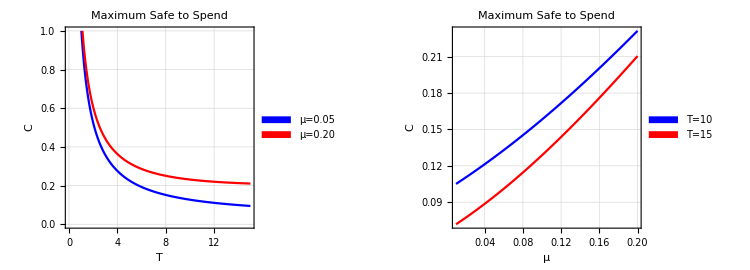

```mathematica
maxSafeSpend1= Plot[{maxC[0.05,T],maxC[0.20,T]},{T,0.01,15},
PlotStyle->{Blue,Red},
PlotLabel->"Maximum Safe to Spend",
PlotLegends->Placed[SwatchLegend[{"μ=0.05","μ=0.20"}],{0.87,0.88}],
FrameLabel->{"T","C"},
Frame->True,
GridLines->Automatic,
PlotRange->{{0,15},{0,1}}];
maxSafeSpend2= Plot[{maxC[μ,10],maxC[μ,15]},{μ,0.01,0.20},
PlotStyle->{Blue,Red},
PlotLabel->"Maximum Safe to Spend",
PlotLegends->Placed[SwatchLegend[{"T=10","T=15"}],{0.13,0.88}],
FrameLabel->{"μ","C"},
Frame->True,
GridLines->Automatic,
PlotRange->{{0.01,0.20},{Min[maxC[0.01,10],maxC[0.01,15]],Max[maxC[0.20,10],maxC[0.20,15]]}}];
maxSafeSpend=GraphicsGrid[{{maxSafeSpend1,maxSafeSpend2}},ImageSize->{750,270}]
Export["images/max-safe-spend.jpeg",maxSafeSpend];
```

### (iv)

Clear variables

```mathematica
Clear["Global`*"]
```

ODE wealth - consumption

```mathematica
DSolve[{a'[t]+(μ*(ψ-1)-δ*ψ)*a[t]+1==0,a[T]==1},a[t],t]//FullSimplify
```

{{a[t]→(1+ⅇ^(-((t-T) (μ (-1+ψ)-δ ψ))) (-1+μ+δ ψ-μ ψ))/(μ+δ ψ-μ ψ)}}

### (vi)

Consumption - savings ratio

```mathematica
cS[δ_,ψ_,μ_,t_,T_]:=(μ*(ψ-1)-δ*ψ)/(ⅇ^((μ*(ψ-1)-δ*ψ)*(T-t))*(1+μ*(ψ-1)-δ*ψ)-1-μ*(ψ-1)+δ*ψ)
```

Plot the consumption - savings ratio

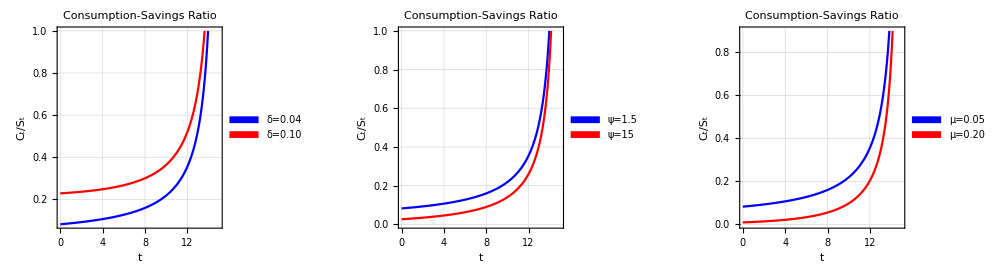

```mathematica
cSδ= Plot[{cS[0.04,2.5,0.05,t,15],cS[0.10,2.5,0.05,t,15]},{t,0,15},
PlotStyle->{Blue,Red},
PlotLabel->"Consumption-Savings Ratio",
PlotLegends->Placed[SwatchLegend[{"δ=0.04","δ=0.10"}],{0.12,0.88}],
FrameLabel->{"t","C_t/S_t"},
Frame->True,
GridLines->Automatic,
PlotRange->{{0,15},{Automatic,1}}];
cSψ= Plot[{cS[0.04,2.5,0.05,t,15],cS[0.04,15,0.05,t,15]},{t,0,15},
PlotStyle->{Blue,Red},
PlotLabel->"Consumption-Savings Ratio",
PlotLegends->Placed[SwatchLegend[{"ψ=1.5","ψ=15"}],{0.12,0.88}],
FrameLabel->{"t","C_t/S_t"},
Frame->True,
GridLines->Automatic,
PlotRange->{{0,15},{Automatic,1}}];
cSμ= Plot[{cS[0.04,2.5,0.05,t,15],cS[0.04,2.5,0.20,t,15]},{t,0,15},
PlotStyle->{Blue,Red},
PlotLabel->"Consumption-Savings Ratio",
PlotLegends->Placed[SwatchLegend[{"μ=0.05","μ=0.20"}],{0.12,0.88}],
FrameLabel->{"t","C_t/S_t"},
Frame->True,
GridLines->Automatic,
PlotRange->{{0,15},{Automatic,0.9}}];
consumptionSavings=GraphicsGrid[{{cSδ,cSψ,cSμ}},ImageSize->{1000,270}]
Export["images/consumption-savings.jpeg",consumptionSavings];
```

## Question 3

### (i)

Clear variables

```mathematica
Clear["Global`*"]
```

ODE savings rate

```mathematica
DSolve[{μ'[t]==κ*(θ-μ[t]),μ[0]==μ0},μ[t],t]//FullSimplify
```

{{μ[t]→θ+ⅇ^(-t κ) (-θ+μ0)}}

ODE wealth - consumption

```mathematica
DSolve[{0==a'[μ]*κ*(θ-μ)+(μ*(ψ-1)-δ*ψ)*a[μ]+1},a[μ],μ]//FullSimplify
```

{{a[μ]→ⅇ^((μ (-1+ψ))/κ) ((-θ+μ)^(-(θ+δ ψ-θ ψ)/κ) C[1]-(ⅇ^((θ-θ ψ)/κ) ExpIntegralE[(κ+θ (-1+ψ)-δ ψ)/κ,((-θ+μ) (-1+ψ))/κ])/κ)}}

## Question 4

### (v)

Clear variables

```mathematica
Clear["Global`*"]
```

Capital per worker

```mathematica
k[t_,k0_]:=(k0^(1-α) *ⅇ^(-a *t)+s/(δ+n)(1-ⅇ^(-a *t)))^(1/(1-α))/.a->(1-α)*( δ+n)
```

Output per worker

```mathematica
y[t_,k0_]:=k[t,k0]^α
```

Consumption per worker

```mathematica
CapitalLabor=Plot[{k[t,3]/.{α->1/3,n->.01,δ->.05,s->.1},k[t,2.5]/.{α->1/3,n->.01,δ->.05,s->.1},k[t,2]/.{α->1/3,n->.01,δ->.05,s->.1},k[t,1.5]/.{α->1/3,n->.01,δ->.05,s->.1}},{t,0,60},
PlotStyle->{Blue,Red,Green,Magenta},
PlotLabel->"Capital-Labor Ratio",
PlotLegends->Placed[SwatchLegend[{"k_0=3.0","k_0=2.5","k_0=2.0","k_0=1.5"}],{0.87,0.80}],
FrameLabel->{"t","k_t"},
Frame->True,
GridLines->Automatic];
OutputLabor=Plot[{k[t,3]/.{α->1/3,n->.01,δ->.05,s->.1},k[t,2.5]/.{α->1/3,n->.01,δ->.05,s->.1},k[t,2]/.{α->1/3,n->.01,δ->.05,s->.1},k[t,1.5]/.{α->1/3,n->.01,δ->.05,s->.1}},{t,0,60},
PlotStyle->{Blue,Red,Green,Magenta},
PlotLabel->"Capital-Labor Ratio",
PlotLegends->Placed[SwatchLegend[{"k_0=3.0","k_0=2.5","k_0=2.0","k_0=1.5"}],{0.87,0.80}],
FrameLabel->{"t","k_t"},
Frame->True,
GridLines->Automatic];
ConsumptionLabor=Plot[{k[t,3]/.{α->1/3,n->.01,δ->.05,s->.1},k[t,2.5]/.{α->1/3,n->.01,δ->.05,s->.1},k[t,2]/.{α->1/3,n->.01,δ->.05,s->.1},k[t,1.5]/.{α->1/3,n->.01,δ->.05,s->.1}},{t,0,60},
PlotStyle->{Blue,Red,Green,Magenta},
PlotLabel->"Capital-Labor Ratio",
PlotLegends->Placed[SwatchLegend[{"k_0=3.0","k_0=2.5","k_0=2.0","k_0=1.5"}],{0.87,0.80}],
FrameLabel->{"t","k_t"},
Frame->True,
GridLines->Automatic];
Capital=GraphicsGrid[{{CapitalLabor},{OutputLabor},{ConsumptionLabor}},ImageSize->{375,810}]
Export["images/solow-ratios.jpeg",Capital];
```